```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
twistExpSumList[n_, b_, p_, q_] := Prepend[Accumulate[(Exp[2.0*Pi*I*(sumIntDigits[#, b]/p + (#/q))]&/@Range[n])], 0]
twistVisualizer[n_, b_, p_, q_]:=ListLinePlot[ReIm /@ twistExpSumList[n,b, p, q], PlotStyle->Thick]
expSumList[n_ ,b_, p_]:=Prepend[Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]], 0]
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p], PlotStyle->Thick]
chunkVisualizer[n1_, n2_, b_, p_, c_]:=ListLinePlot[ReIm /@ Take[expSumList[n2,b, p], {n1, n2+1}], PlotStyle->{Thick, c}]
pointVisualizer[n_, b_, p_]:=ListPlot[ReIm /@ expSumList[n,b, p], PlotStyle->{PointSize[Large], Red}]
```

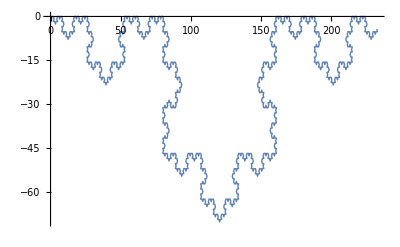

```mathematica
twistVisualizer[1000, 2, 2, 3]
```

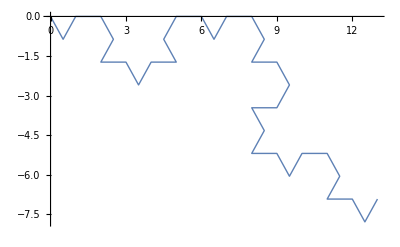
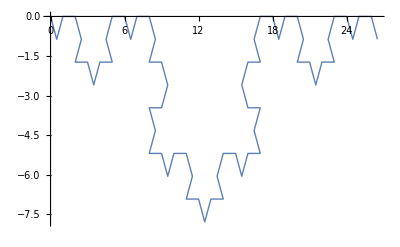
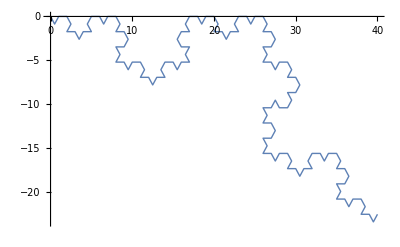
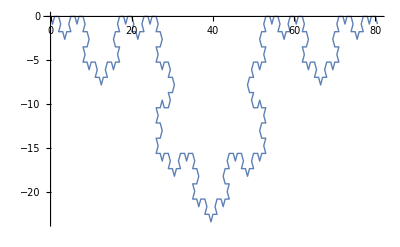
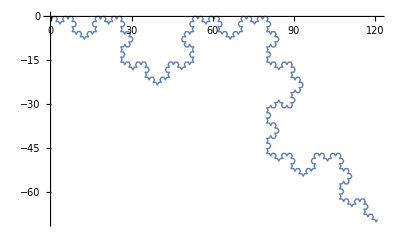
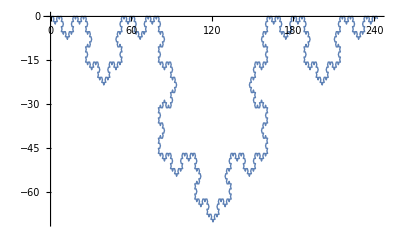
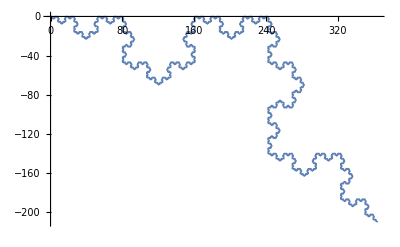
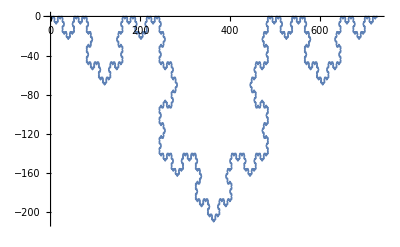

```mathematica
Table[twistVisualizer[2^k, 2, 2, 3], {k, 5, 15}]
```

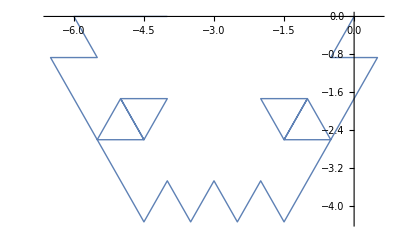
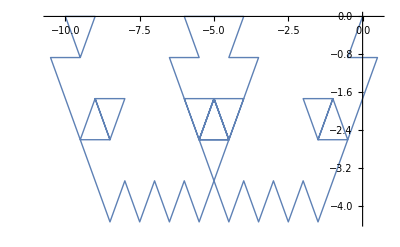
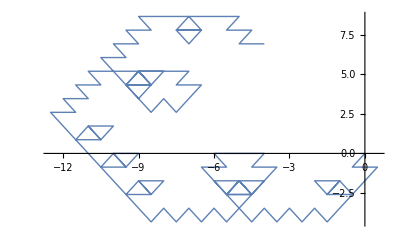
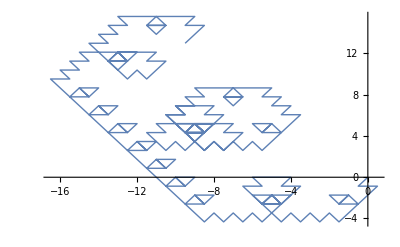
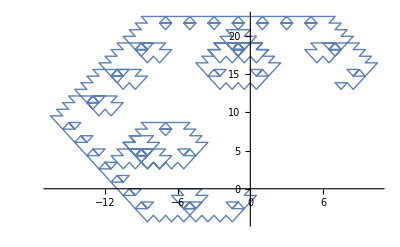
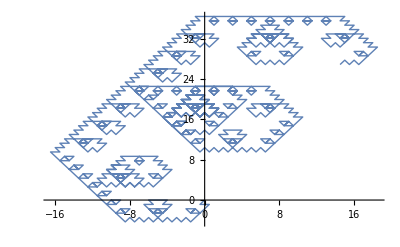
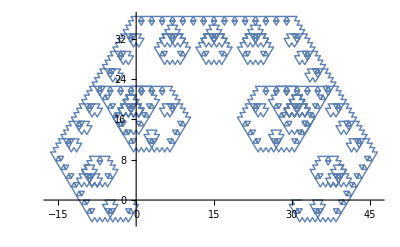
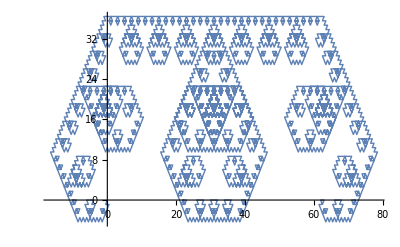

```mathematica
Table[twistVisualizer[2^k, 2, 3, 3], {k, 5, 15}]
```

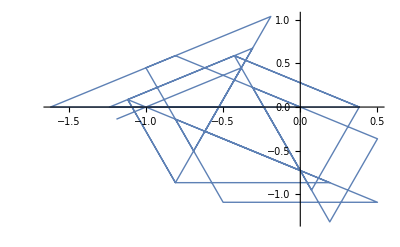
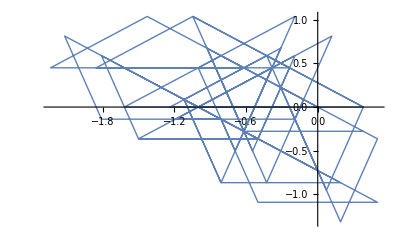
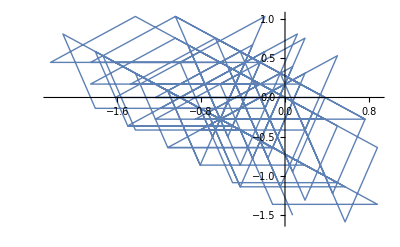
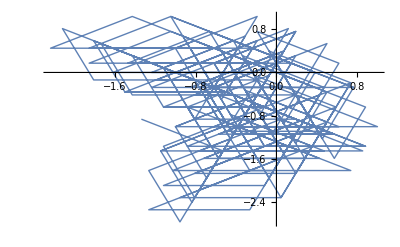
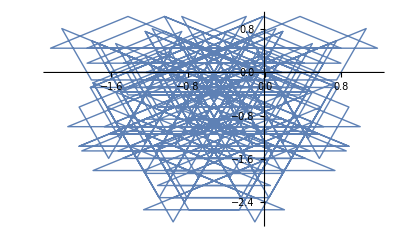
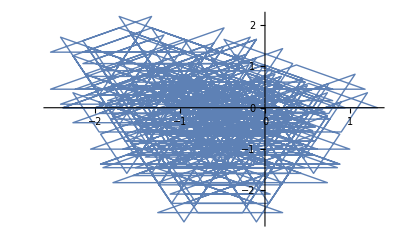
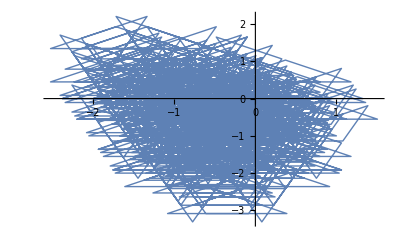
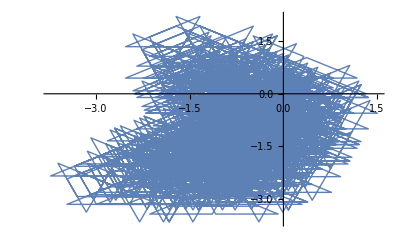

```mathematica
Table[twistVisualizer[2^k, 2, 5, 5], {k, 5, 15}]
```

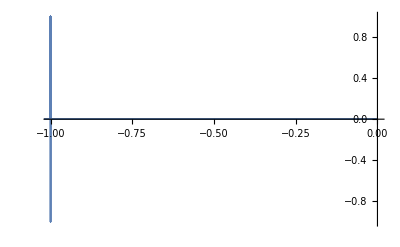
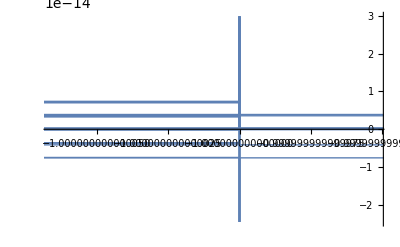
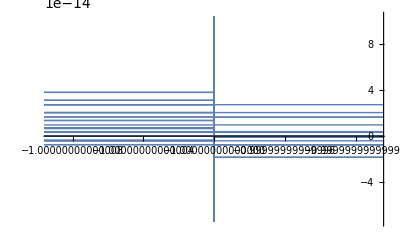
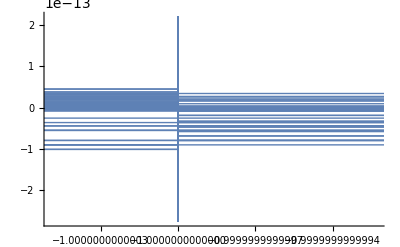
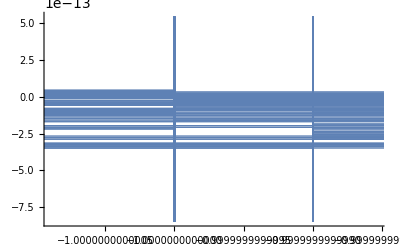
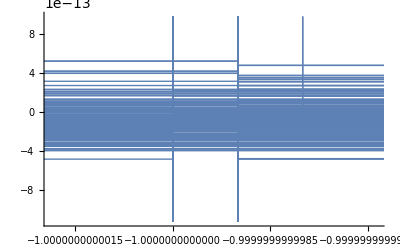
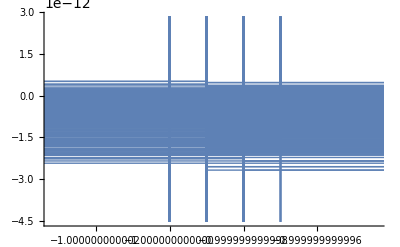
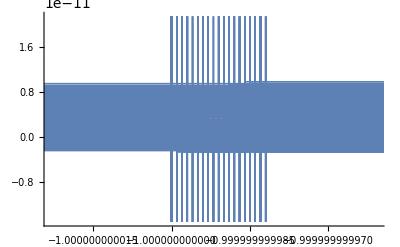
{{{{32,3},-Graphics-},{{64,3},-Graphics-},{{128,3},-Graphics-},{{256,3},-Graphics-},{{512,3},-Graphics-},{{1024,3},-Graphics-},{{2048,3},-Graphics-},{{4096,3},-Graphics-}},{{{32,4},-Graphics-},{{64,4},-Graphics-},{{128,4},-Graphics-},{{256,4},-Graphics-},{{512,4},-Graphics-},{{1024,4},-Graphics-},{{2048,4},-Graphics-},{{4096,4},-Graphics-}},{{{32,5},-Graphics-},{{64,5},-Graphics-},{{128,5},-Graphics-},{{256,5},-Graphics-},{{512,5},-Graphics-},{{1024,5},-Graphics-},{{2048,5},-Graphics-},{{4096,5},-Graphics-}},{{{32,6},-Graphics-},{{64,6},-Graphics-},{{128,6},-Graphics-},{{256,6},-Graphics-},{{512,6},-Graphics-},{{1024,6},-Graphics-},{{2048,6},-Graphics-},{{4096,6},-Graphics-}},{{{32,7},-Graphics-},{{64,7},-Graphics-},{{128,7},-Graphics-},{{256,7},-Graphics-},{{512,7},-Graphics-},{{1024,7},-Graphics-},{{2048,7},-Graphics-},{{4096,7},-Graphics-}},{{{32,8},-Graphics-},{{64,8},-Graphics-},{{128,8},-Graphics-},{{256,8},-Graphics-},{{512,8},-Graphics-},{{1024,8},-Graphics-},{{2048,8},-Graphics-},{{4096,8},-Graphics-}},{{{32,9},-Graphics-},{{64,9},-Graphics-},{{128,9},-Graphics-},{{256,9},-Graphics-},{{512,9},-Graphics-},{{1024,9},-Graphics-},{{2048,9},-Graphics-},{{4096,9},-Graphics-}},{{{32,10},-Graphics-},{{64,10},-Graphics-},{{128,10},-Graphics-},{{256,10},-Graphics-},{{512,10},-Graphics-},{{1024,10},-Graphics-},{{2048,10},-Graphics-},{{4096,10},-Graphics-}},{{{32,11},-Graphics-},{{64,11},-Graphics-},{{128,11},-Graphics-},{{256,11},-Graphics-},{{512,11},-Graphics-},{{1024,11},-Graphics-},{{2048,11},-Graphics-},{{4096,11},-Graphics-}},{{{32,12},-Graphics-},{{64,12},-Graphics-},{{128,12},-Graphics-},{{256,12},-Graphics-},{{512,12},-Graphics-},{{1024,12},-Graphics-},{{2048,12},-Graphics-},{{4096,12},-Graphics-}},{{{32,13},-Graphics-},{{64,13},-Graphics-},{{128,13},-Graphics-},{{256,13},-Graphics-},{{512,13},-Graphics-},{{1024,13},-Graphics-},{{2048,13},-Graphics-},{{4096,13},-Graphics-}},{{{32,14},-Graphics-},{{64,14},-Graphics-},{{128,14},-Graphics-},{{256,14},-Graphics-},{{512,14},-Graphics-},{{1024,14},-Graphics-},{{2048,14},-Graphics-},{{4096,14},-Graphics-}},{{{32,15},-Graphics-},{{64,15},-Graphics-},{{128,15},-Graphics-},{{256,15},-Graphics-},{{512,15},-Graphics-},{{1024,15},-Graphics-},{{2048,15},-Graphics-},{{4096,15},-Graphics-}}}

```mathematica
Table[{{2^k, q},twistVisualizer[2^k, 2, q, q]}, {q, 3, 15}, {k, 5, 12}]
```

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
qList = RandomReal[{2, 5}, 10]
```

{2.33426,4.36858,2.56341,2.72408,2.19722,3.62674,2.69346,3.18802,4.10142,2.63548}

```mathematica
Table[{2^k, q, twistVisualizer[2^k, 2, q, q]},{q, qList},{k, 5, 12}]
```

{{{32,2.33426,-Graphics-},{64,2.33426,-Graphics-},{128,2.33426,-Graphics-},{256,2.33426,-Graphics-},{512,2.33426,-Graphics-},{1024,2.33426,-Graphics-},{2048,2.33426,-Graphics-},{4096,2.33426,-Graphics-}},{{32,4.36858,-Graphics-},{64,4.36858,-Graphics-},{128,4.36858,-Graphics-},{256,4.36858,-Graphics-},{512,4.36858,-Graphics-},{1024,4.36858,-Graphics-},{2048,4.36858,-Graphics-},{4096,4.36858,-Graphics-}},{{32,2.56341,-Graphics-},{64,2.56341,-Graphics-},{128,2.56341,-Graphics-},{256,2.56341,-Graphics-},{512,2.56341,-Graphics-},{1024,2.56341,-Graphics-},{2048,2.56341,-Graphics-},{4096,2.56341,-Graphics-}},{{32,2.72408,-Graphics-},{64,2.72408,-Graphics-},{128,2.72408,-Graphics-},{256,2.72408,-Graphics-},{512,2.72408,-Graphics-},{1024,2.72408,-Graphics-},{2048,2.72408,-Graphics-},{4096,2.72408,-Graphics-}},{{32,2.19722,-Graphics-},{64,2.19722,-Graphics-},{128,2.19722,-Graphics-},{256,2.19722,-Graphics-},{512,2.19722,-Graphics-},{1024,2.19722,-Graphics-},{2048,2.19722,-Graphics-},{4096,2.19722,-Graphics-}},{{32,3.62674,-Graphics-},{64,3.62674,-Graphics-},{128,3.62674,-Graphics-},{256,3.62674,-Graphics-},{512,3.62674,-Graphics-},{1024,3.62674,-Graphics-},{2048,3.62674,-Graphics-},{4096,3.62674,-Graphics-}},{{32,2.69346,-Graphics-},{64,2.69346,-Graphics-},{128,2.69346,-Graphics-},{256,2.69346,-Graphics-},{512,2.69346,-Graphics-},{1024,2.69346,-Graphics-},{2048,2.69346,-Graphics-},{4096,2.69346,-Graphics-}},{{32,3.18802,-Graphics-},{64,3.18802,-Graphics-},{128,3.18802,-Graphics-},{256,3.18802,-Graphics-},{512,3.18802,-Graphics-},{1024,3.18802,-Graphics-},{2048,3.18802,-Graphics-},{4096,3.18802,-Graphics-}},{{32,4.10142,-Graphics-},{64,4.10142,-Graphics-},{128,4.10142,-Graphics-},{256,4.10142,-Graphics-},{512,4.10142,-Graphics-},{1024,4.10142,-Graphics-},{2048,4.10142,-Graphics-},{4096,4.10142,-Graphics-}},{{32,2.63548,-Graphics-},{64,2.63548,-Graphics-},{128,2.63548,-Graphics-},{256,2.63548,-Graphics-},{512,2.63548,-Graphics-},{1024,2.63548,-Graphics-},{2048,2.63548,-Graphics-},{4096,2.63548,-Graphics-}}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 2.97422, 2.97422]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 3, 3]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 113/38, 113/38]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Manipulate[list = ReIm /@ twistExpSumList[2^k, 2, 2.97422, 2.97422];
maxRange  = 1.1*Max[Abs[list]];
ListLinePlot[Take[list, Floor[2^k]],PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, AspectRatio->1],{k, 5, 15,Animator, AnimationRate->1, AnimationRunning->True}]
```

```mathematica
Table[{twistVisualizer[5000, 2, q, q]}, {q, 3, 15}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Table[{twistVisualizer[5000, 2, 2, q]}, {q, 3, 15}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
irrationalList = {Sqrt[2], Sqrt[3], Sqrt[6], Pi, EulerGamma, Log[2.], E}
```

{√2,√3,√6,π,EulerGamma,0.693147,ⅇ}

```mathematica
Table[twistVisualizer[5000, 3, 2, q], {q, irrationalList}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
N[E]
```

2.71828

```mathematica
Table[{b, twistVisualizer[5000, b, 2, q]}, {b, 2, 10}, {q, irrationalList}]
```

{{{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-}},{{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-}},{{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-}},{{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-}},{{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-}},{{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-}},{{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-}},{{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-}},{{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-}}}

```mathematica
Manipulate[twistVisualizer[5000, b, 2, q], {b, 2, 10, 1,SetterBar}, {q, irrationalList, SetterBar}]
```

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
(* Overall, trying to see if pattern of odd bases is a single circle for any q *)
Table[twistVisualizer[3000, 5, 2, q], {q, 2, 15,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Here we can see that if we generate random real numbers, the pattern is holding to an extent *)
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, RandomReal[{1, 10}, 10]}]
```

{{7.73791,-Graphics-},{4.80566,-Graphics-},{3.22745,-Graphics-},{9.79455,-Graphics-},{8.42647,-Graphics-},{9.32748,-Graphics-},{6.20251,-Graphics-},{3.63583,-Graphics-},{2.87246,-Graphics-},{6.22427,-Graphics-}}

We can see here so far that actual integers are not creating the circles we need for some reason, and that rather, it is some random real numbers that are indeed doing the trick. So far, I will hypothesize that the number needs to be a decimal for this pattern to hold. Now, onto negative numbers.

```mathematica
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, RandomReal[{-10, -1}, 10]}]
```

{{-8.84061,-Graphics-},{-7.24215,-Graphics-},{-3.59189,-Graphics-},{-6.48476,-Graphics-},{-2.62029,-Graphics-},{-7.07184,-Graphics-},{-4.66066,-Graphics-},{-5.33103,-Graphics-},{-8.47888,-Graphics-},{-5.74691,-Graphics-}}

This pattern also appears to work with negative numbers (I actually ran a lot more tests with this than I’ve shown). So, now we need to actually prove that there is some special properties with these decimals that are creating this circular visualizations, as opposed to the other convex shapes we get when we run this code for integers.

```mathematica
(* Testing the digits of the decimal values *)
randomlist = RandomReal[{-10, 10}, 10]
```

{6.14322,-9.76329,-3.66248,5.79608,-9.76044,-2.17447,-0.821956,-0.823102,4.55034,5.81133}

```mathematica
sumlist = Total[#]& /@ (First /@ RealDigits[randomlist])
```

{63,71,78,70,83,59,64,55,72,48}

```mathematica
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, randomlist}]
```

{{6.14322,-Graphics-},{-9.76329,-Graphics-},{-3.66248,-Graphics-},{5.79608,-Graphics-},{-9.76044,-Graphics-},{-2.17447,-Graphics-},{-0.821956,-Graphics-},{-0.823102,-Graphics-},{4.55034,-Graphics-},{5.81133,-Graphics-}}

Currently, I really can not find a pattern as to why this is the way it is, but I will continue to experiment in the future, because this is an interesting pattern.

```mathematica
Mod[#,5]& /@ sumlist
```

{3,1,3,0,3,4,4,0,2,3}

```mathematica
colorlist=Table[Hue[0.15+i/400],{i,1,400}]
```

{Hue[0.1525],Hue[0.155],Hue[0.1575],Hue[0.16],Hue[0.1625],Hue[0.16499999999999998],Hue[0.16749999999999998],Hue[0.16999999999999998],Hue[0.1725],Hue[0.175],Hue[0.1775],Hue[0.18],Hue[0.1825],Hue[0.185],Hue[0.1875],Hue[0.19],Hue[0.1925],Hue[0.195],Hue[0.1975],Hue[0.2],Hue[0.20249999999999999],Hue[0.205],Hue[0.2075],Hue[0.21],Hue[0.2125],Hue[0.215],Hue[0.2175],Hue[0.22],Hue[0.22249999999999998],Hue[0.22499999999999998],Hue[0.22749999999999998],Hue[0.22999999999999998],Hue[0.23249999999999998],Hue[0.235],Hue[0.2375],Hue[0.24],Hue[0.2425],Hue[0.245],Hue[0.2475],Hue[0.25],Hue[0.2525],Hue[0.255],Hue[0.2575],Hue[0.26],Hue[0.2625],Hue[0.265],Hue[0.26749999999999996],Hue[0.27],Hue[0.27249999999999996],Hue[0.275],Hue[0.27749999999999997],Hue[0.28],Hue[0.2825],Hue[0.28500000000000003],Hue[0.2875],Hue[0.29000000000000004],Hue[0.2925],Hue[0.295],Hue[0.2975],Hue[0.3],Hue[0.3025],Hue[0.305],Hue[0.3075],Hue[0.31],Hue[0.3125],Hue[0.315],Hue[0.3175],Hue[0.32],Hue[0.3225],Hue[0.32499999999999996],Hue[0.3275],Hue[0.32999999999999996],Hue[0.3325],Hue[0.33499999999999996],Hue[0.3375],Hue[0.33999999999999997],Hue[0.3425],Hue[0.345],Hue[0.34750000000000003],Hue[0.35],Hue[0.35250000000000004],Hue[0.355],Hue[0.3575],Hue[0.36],Hue[0.3625],Hue[0.365],Hue[0.3675],Hue[0.37],Hue[0.3725],Hue[0.375],Hue[0.3775],Hue[0.38],Hue[0.3825],Hue[0.385],Hue[0.38749999999999996],Hue[0.39],Hue[0.39249999999999996],Hue[0.395],Hue[0.39749999999999996],Hue[0.4],Hue[0.40249999999999997],Hue[0.405],Hue[0.4075],Hue[0.41000000000000003],Hue[0.4125],Hue[0.41500000000000004],Hue[0.4175],Hue[0.42000000000000004],Hue[0.4225],Hue[0.42500000000000004],Hue[0.4275],Hue[0.43000000000000005],Hue[0.4325],Hue[0.43499999999999994],Hue[0.4375],Hue[0.43999999999999995],Hue[0.4425],Hue[0.44499999999999995],Hue[0.4475],Hue[0.44999999999999996],Hue[0.4525],Hue[0.45499999999999996],Hue[0.4575],Hue[0.45999999999999996],Hue[0.4625],Hue[0.46499999999999997],Hue[0.4675],Hue[0.47],Hue[0.47250000000000003],Hue[0.475],Hue[0.47750000000000004],Hue[0.48],Hue[0.48250000000000004],Hue[0.485],Hue[0.48750000000000004],Hue[0.49],Hue[0.49250000000000005],Hue[0.495],Hue[0.49749999999999994],Hue[0.5],Hue[0.5025],Hue[0.505],Hue[0.5075],Hue[0.51],Hue[0.5125],Hue[0.515],Hue[0.5175],Hue[0.52],Hue[0.5225],Hue[0.525],Hue[0.5275],Hue[0.53],Hue[0.5325],Hue[0.535],Hue[0.5375],Hue[0.54],Hue[0.5425],Hue[0.545],Hue[0.5475],Hue[0.55],Hue[0.5525],Hue[0.555],Hue[0.5575],Hue[0.5599999999999999],Hue[0.5625],Hue[0.565],Hue[0.5675],Hue[0.57],Hue[0.5725],Hue[0.575],Hue[0.5775],Hue[0.58],Hue[0.5825],Hue[0.585],Hue[0.5875],Hue[0.59],Hue[0.5925],Hue[0.595],Hue[0.5975],Hue[0.6],Hue[0.6025],Hue[0.605],Hue[0.6075],Hue[0.61],Hue[0.6125],Hue[0.615],Hue[0.6175],Hue[0.62],Hue[0.6224999999999999],Hue[0.625],Hue[0.6275],Hue[0.63],Hue[0.6325],Hue[0.635],Hue[0.6375],Hue[0.64],Hue[0.6425],Hue[0.645],Hue[0.6475],Hue[0.65],Hue[0.6525],Hue[0.655],Hue[0.6575],Hue[0.66],Hue[0.6625],Hue[0.665],Hue[0.6675],Hue[0.67],Hue[0.6725],Hue[0.675],Hue[0.6775],Hue[0.68],Hue[0.6825],Hue[0.685],Hue[0.6875],Hue[0.6900000000000001],Hue[0.6925],Hue[0.6950000000000001],Hue[0.6975],Hue[0.7000000000000001],Hue[0.7025],Hue[0.7050000000000001],Hue[0.7075],Hue[0.7100000000000001],Hue[0.7125],Hue[0.715],Hue[0.7175],Hue[0.72],Hue[0.7225],Hue[0.725],Hue[0.7275],Hue[0.73],Hue[0.7325],Hue[0.735],Hue[0.7375],Hue[0.74],Hue[0.7425],Hue[0.745],Hue[0.7475],Hue[0.75],Hue[0.7525000000000001],Hue[0.755],Hue[0.7575000000000001],Hue[0.76],Hue[0.7625000000000001],Hue[0.765],Hue[0.7675000000000001],Hue[0.77],Hue[0.7725000000000001],Hue[0.775],Hue[0.7775],Hue[0.78],Hue[0.7825],Hue[0.785],Hue[0.7875],Hue[0.79],Hue[0.7925],Hue[0.795],Hue[0.7975],Hue[0.8],Hue[0.8025],Hue[0.805],Hue[0.8075],Hue[0.81],Hue[0.8125],Hue[0.8150000000000001],Hue[0.8175],Hue[0.8200000000000001],Hue[0.8225],Hue[0.8250000000000001],Hue[0.8275],Hue[0.8300000000000001],Hue[0.8325],Hue[0.8350000000000001],Hue[0.8375],Hue[0.84],Hue[0.8425],Hue[0.845],Hue[0.8475],Hue[0.85],Hue[0.8525],Hue[0.855],Hue[0.8575],Hue[0.86],Hue[0.8625],Hue[0.865],Hue[0.8675],Hue[0.87],Hue[0.8725],Hue[0.875],Hue[0.8775000000000001],Hue[0.88],Hue[0.8825000000000001],Hue[0.885],Hue[0.8875000000000001],Hue[0.89],Hue[0.8925000000000001],Hue[0.895],Hue[0.8975000000000001],Hue[0.9],Hue[0.9025],Hue[0.905],Hue[0.9075],Hue[0.91],Hue[0.9125],Hue[0.915],Hue[0.9175],Hue[0.92],Hue[0.9225],Hue[0.925],Hue[0.9275],Hue[0.93],Hue[0.9325],Hue[0.935],Hue[0.9375],Hue[0.9400000000000001],Hue[0.9425],Hue[0.9450000000000001],Hue[0.9475],Hue[0.9500000000000001],Hue[0.9525],Hue[0.9550000000000001],Hue[0.9575],Hue[0.9600000000000001],Hue[0.9625],Hue[0.965],Hue[0.9675],Hue[0.97],Hue[0.9725],Hue[0.975],Hue[0.9775],Hue[0.98],Hue[0.9825],Hue[0.985],Hue[0.9875],Hue[0.99],Hue[0.9925],Hue[0.995],Hue[0.9975],Hue[1.],Hue[1.0025],Hue[1.005],Hue[1.0075],Hue[1.01],Hue[1.0125],Hue[1.015],Hue[1.0175],Hue[1.02],Hue[1.0225],Hue[1.025],Hue[1.0274999999999999],Hue[1.03],Hue[1.0325],Hue[1.035],Hue[1.0374999999999999],Hue[1.04],Hue[1.0425],Hue[1.045],Hue[1.0474999999999999],Hue[1.05],Hue[1.0525],Hue[1.055],Hue[1.0574999999999999],Hue[1.06],Hue[1.0625],Hue[1.065],Hue[1.0675],Hue[1.07],Hue[1.0725],Hue[1.075],Hue[1.0775],Hue[1.08],Hue[1.0825],Hue[1.085],Hue[1.0875],Hue[1.0899999999999999],Hue[1.0925],Hue[1.095],Hue[1.0975],Hue[1.0999999999999999],Hue[1.1025],Hue[1.105],Hue[1.1075],Hue[1.1099999999999999],Hue[1.1125],Hue[1.115],Hue[1.1175],Hue[1.1199999999999999],Hue[1.1225],Hue[1.125],Hue[1.1275],Hue[1.13],Hue[1.1325],Hue[1.135],Hue[1.1375],Hue[1.14],Hue[1.1425],Hue[1.145],Hue[1.1475],Hue[1.15]}

```mathematica
Manipulate[ 
twistList = ReIm /@ twistExpSumList[5000, b, p, q];
Graphics[{Thick,
Line[Take[twistList,n],
VertexColors->colorlist]},
Axes->True,ImageSize->Large,Background->Black
],
{n,1,400,1},
{b, 3, 15, 1},
{p, 3, 20, 1},
{q, 1, 20, 1}]
```

```mathematica
Manipulate[ 
SeedRandom[seed];
maxSteps = 1500;
colorlist=Table[Hue[0.15+i/maxSteps],{i,1,maxSteps}];
q = Sqrt[RandomPrime[100]];
twistList = ReIm /@ twistExpSumList[n, b, p, q];
maxRange = 1.1*Max[Abs[twistList]];
Graphics[{Thick,
Line[Take[twistList, n],
VertexColors->colorlist]},
Axes->True,ImageSize->Large,Background->Black, PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, PlotLabel->{q}
],
(*{n,1,1500,1, Animator, AnimationRate->100, AnimationRunning->True}, *)
Control@{{n,1,"animate"},maxSteps,1,-1,Trigger},
{b, 3, 15, 1, SetterBar},
{p, 3, 20, 1, SetterBar},
{seed, 1, 1000, 1, Appearance->Labeled},
Button["Randomize", seed = Mod[(seed+1)*2011 , 1000]; n = 1]]
```

```mathematica
Manipulate[ 
SeedRandom[seed];
maxSteps = 1500;
kdelta = 0.2;
colorlist=Table[Hue[0.25+i/maxSteps],{i,1,maxSteps}];
q = RandomReal[{3, 10}];
n = Floor[2^k];
twistList = ReIm /@ twistExpSumList[n, b, p, q];
maxRange = 1.1*Max[Abs[twistList]];
bgcolor = If[color === colorlist, Black, White];
Graphics[{Thick,
Line[Take[twistList, n],
VertexColors->color]},
Axes->True,ImageSize->Large,Background->bgcolor, PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, PlotLabel->"q ="+q
],
{k, 1, 10, kdelta},
Control@{{k,1,"animate"},1,10,0.1,Trigger},
{{b,3, "base"}, 3, 15, 1, SetterBar},
{p, 3, 20, 1, SetterBar},
{seed, 1, 1000, 1, Appearance->Labeled},
{color,{colorlist->"Rainbow", Black->"Basic"}},
Button["Randomize", seed = Mod[(seed++)*2011 , 1000]; k = 10; n = 2^10;Pause[0.01]]]
```

```mathematica
mastermanip[] :=
Manipulate[
SeedRandom[seed];
kmax=N[Log[2,maxSteps]];
If[k>kmax,k=kmax];(*out of range error trick*)
kdelta=0.1;
colorlist=Table[Hue[0.25+i/maxSteps],{i,1,maxSteps}];
currentsteps=Floor[2^k];
irr={Pi,E,GoldenRatio->"φ",Pi^2,Log[2]->"ln(2)",Sqrt[2],Sqrt[3]};
points=ReIm/@twistExpSumList[maxSteps,b,p,q];
currentpoints=Take[points,maxSteps-currentsteps+1];
maxRange=If[scale,1.1*Max[Abs[points]],1.1*Max[Abs[currentpoints]]];
bgcolor=If[color,Black,White];
labelcolor = If[color, Yellow, Black];
plotlabel = Row[{"Exponential Sum Walk with b = ", b, ", p = ", p, ", q = ", q}];

Graphics[
{Thick,If[color,Line[currentpoints,VertexColors->colorlist],
Line[currentpoints]]},
Axes->True,
ImageSize->Large,
Background->bgcolor,
PlotRange->{{-maxRange,maxRange},{-maxRange,maxRange}},
PlotLabel->Style[plotlabel,15,labelcolor]
],

{{maxSteps,1500},{100,1500,3000,5000},SetterBar},
Control@{{k,1,"animate"},kmax,1,-kdelta,Trigger},
{{color,True},{True,False},Checkbox},
{{scale,False,"fixed scale"},{True,False},Checkbox},

Delimiter,
Style["base", 13],
{{b,2,""},2,12,1,SetterBar},

Delimiter,
Style["control p", 13],
(* Controls for p *)
{{p,3, ""},2,12,1,SetterBar},
{{p, Pi, ""},irr,SetterBar},
Button[Style["Randomize p",FontColor->Black],seed++;p=RandomReal[{3,10}],ImageSize->200],

Delimiter,
Style["control q", 13],
(* Controls for q *)
Control@{{q,3, ""},2,12,1,SetterBar},
{{q,Pi, ""},irr,SetterBar},
Button[Style["Randomize q",FontColor->Black],seed++;q=RandomReal[{3,10}],ImageSize->200],
{seed,1,1000,1,ControlType->None},
ControlPlacement->Left
];
```

```mathematica
mastermanip[]
```